```mathematica
FindFullFormula[Graph[Range[5],{}]]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x2x345,v1x25x3x4,v1x25x34,v1x24x3x5,v1x245x3,v1x24x35,v1x23x4x5,v1x235x4,v1x234x5,v1x23x45,v1x2345,v15x2x3x4,v15x2x34,v15x24x3,v15x23x4,v15x234,v14x2x3x5,v145x2x3,v14x2x35,v14x25x3,v14x23x5,v14x235,v145x23,v13x2x4x5,v135x2x4,v134x2x5,v13x2x45,v1345x2,v13x25x4,v134x25,v13x24x5,v13x245,v135x24,v12x3x4x5,v125x3x4,v124x3x5,v12x3x45,v1245x3,v123x4x5,v123x45,v12x35x4,v1235x4,v124x35,v12x34x5,v1234x5,v12x345,v125x34,v12345}

```mathematica
lattice=FormulaGraphReverse2[FindFullFormula[Graph[Range[7],{}]]];
```

```mathematica
EdgeList[lattice]
```

{v1234x5->v12345,v1235x4->v12345,v123x45->v12345,v1245x3->v12345,v124x35->v12345,v125x34->v12345,v12x345->v12345,v1345x2->v12345,v134x25->v12345,v135x24->v12345,v13x245->v12345,v145x23->v12345,v14x235->v12345,v15x234->v12345,v1x2345->v12345,v123x4x5->v1234x5,v124x3x5->v1234x5,v12x34x5->v1234x5,v134x2x5->v1234x5,v13x24x5->v1234x5,v14x23x5->v1234x5,v1x234x5->v1234x5,v123x4x5->v1235x4,v125x3x4->v1235x4,v12x35x4->v1235x4,v135x2x4->v1235x4,v13x25x4->v1235x4,v15x23x4->v1235x4,v1x235x4->v1235x4,v123x4x5->v123x45,v12x3x45->v123x45,v13x2x45->v123x45,v1x23x45->v123x45,v12x3x4x5->v123x4x5,v13x2x4x5->v123x4x5,v1x23x4x5->v123x4x5,v124x3x5->v1245x3,v125x3x4->v1245x3,v12x3x45->v1245x3,v145x2x3->v1245x3,v14x25x3->v1245x3,v15x24x3->v1245x3,v1x245x3->v1245x3,v124x3x5->v124x35,v12x35x4->v124x35,v14x2x35->v124x35,v1x24x35->v124x35,v12x3x4x5->v124x3x5,v14x2x3x5->v124x3x5,v1x24x3x5->v124x3x5,v125x3x4->v125x34,v12x34x5->v125x34,v15x2x34->v125x34,v1x25x34->v125x34,v12x3x4x5->v125x3x4,v15x2x3x4->v125x3x4,v1x25x3x4->v125x3x4,v12x34x5->v12x345,v12x35x4->v12x345,v12x3x45->v12x345,v1x2x345->v12x345,v12x3x4x5->v12x34x5,v1x2x34x5->v12x34x5,v12x3x4x5->v12x35x4,v1x2x35x4->v12x35x4,v12x3x4x5->v12x3x45,v1x2x3x45->v12x3x45,v1x2x3x4x5->v12x3x4x5,v134x2x5->v1345x2,v135x2x4->v1345x2,v13x2x45->v1345x2,v145x2x3->v1345x2,v14x2x35->v1345x2,v15x2x34->v1345x2,v1x2x345->v1345x2,v134x2x5->v134x25,v13x25x4->v134x25,v14x25x3->v134x25,v1x25x34->v134x25,v13x2x4x5->v134x2x5,v14x2x3x5->v134x2x5,v1x2x34x5->v134x2x5,v135x2x4->v135x24,v13x24x5->v135x24,v15x24x3->v135x24,v1x24x35->v135x24,v13x2x4x5->v135x2x4,v15x2x3x4->v135x2x4,v1x2x35x4->v135x2x4,v13x24x5->v13x245,v13x25x4->v13x245,v13x2x45->v13x245,v1x245x3->v13x245,v13x2x4x5->v13x24x5,v1x24x3x5->v13x24x5,v13x2x4x5->v13x25x4,v1x25x3x4->v13x25x4,v13x2x4x5->v13x2x45,v1x2x3x45->v13x2x45,v1x2x3x4x5->v13x2x4x5,v145x2x3->v145x23,v14x23x5->v145x23,v15x23x4->v145x23,v1x23x45->v145x23,v14x2x3x5->v145x2x3,v15x2x3x4->v145x2x3,v1x2x3x45->v145x2x3,v14x23x5->v14x235,v14x25x3->v14x235,v14x2x35->v14x235,v1x235x4->v14x235,v14x2x3x5->v14x23x5,v1x23x4x5->v14x23x5,v14x2x3x5->v14x25x3,v1x25x3x4->v14x25x3,v14x2x3x5->v14x2x35,v1x2x35x4->v14x2x35,v1x2x3x4x5->v14x2x3x5,v15x23x4->v15x234,v15x24x3->v15x234,v15x2x34->v15x234,v1x234x5->v15x234,v15x2x3x4->v15x23x4,v1x23x4x5->v15x23x4,v15x2x3x4->v15x24x3,v1x24x3x5->v15x24x3,v15x2x3x4->v15x2x34,v1x2x34x5->v15x2x34,v1x2x3x4x5->v15x2x3x4,v1x234x5->v1x2345,v1x235x4->v1x2345,v1x23x45->v1x2345,v1x245x3->v1x2345,v1x24x35->v1x2345,v1x25x34->v1x2345,v1x2x345->v1x2345,v1x23x4x5->v1x234x5,v1x24x3x5->v1x234x5,v1x2x34x5->v1x234x5,v1x23x4x5->v1x235x4,v1x25x3x4->v1x235x4,v1x2x35x4->v1x235x4,v1x23x4x5->v1x23x45,v1x2x3x45->v1x23x45,v1x2x3x4x5->v1x23x4x5,v1x24x3x5->v1x245x3,v1x25x3x4->v1x245x3,v1x2x3x45->v1x245x3,v1x24x3x5->v1x24x35,v1x2x35x4->v1x24x35,v1x2x3x4x5->v1x24x3x5,v1x25x3x4->v1x25x34,v1x2x34x5->v1x25x34,v1x2x3x4x5->v1x25x3x4,v1x2x34x5->v1x2x345,v1x2x35x4->v1x2x345,v1x2x3x45->v1x2x345,v1x2x3x4x5->v1x2x34x5,v1x2x3x4x5->v1x2x35x4,v1x2x3x4x5->v1x2x3x45}

```mathematica
ReduceLattice[lattice_]:=Block[{vertexMap=Association[],vertices, edges, edgeLabels},
Monitor[
Table[vertexMap[v]=PartitionType[SymbolToSets[v]],
{v,VertexList[lattice]}
],
{"part 1 : ",v}];
edges=Monitor[Table[
vertexMap[e[[1]]]->vertexMap[e[[2]]]
,{e,EdgeList[lattice]}
],
{"part 2 : ",e}];
edgeLabels=Map[#[[1]]->Placed[Rotate [#[[2]],Pi/4],{Left,"Middle"}]&,Tally[edges]];
Graph[DeleteDuplicates[edges], VertexLabels->"Name",EdgeLabels->edgeLabels, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
Map[#[[1]]->#[[2]]&,[{{{6,1}->{7},7},{{5,2}->{7},21},{{4,3}->{7},35},{{5,1,1}->{6,1},42},{{4,2,1}->{6,1},105},{{3,3,1}->{6,1},70},{{5,1,1}->{5,2},21},{{4,2,1}->{5,2},105},{{3,2,2}->{5,2},210},{{4,1,1,1}->{5,1,1},105},{{3,2,1,1}->{5,1,1},210},{{4,2,1}->{4,3},105},{{3,3,1}->{4,3},140},{{3,2,2}->{4,3},105},{{4,1,1,1}->{4,2,1},105},{{3,2,1,1}->{4,2,1},420},{{2,2,2,1}->{4,2,1},315},{{3,1,1,1,1}->{4,1,1,1},140},{{2,2,1,1,1}->{4,1,1,1},105},{{3,2,1,1}->{3,3,1},420},{{3,2,1,1}->{3,2,2},210},{{2,2,2,1}->{3,2,2},315},{{3,1,1,1,1}->{3,2,1,1},210},{{2,2,1,1,1}->{3,2,1,1},630},{{2,1,1,1,1,1}->{3,1,1,1,1},105},{{2,2,1,1,1}->{2,2,2,1},315},{{2,1,1,1,1,1}->{2,2,1,1,1},210},{{1,1,1,1,1,1,1}->{2,1,1,1,1,1},21}}]]
```

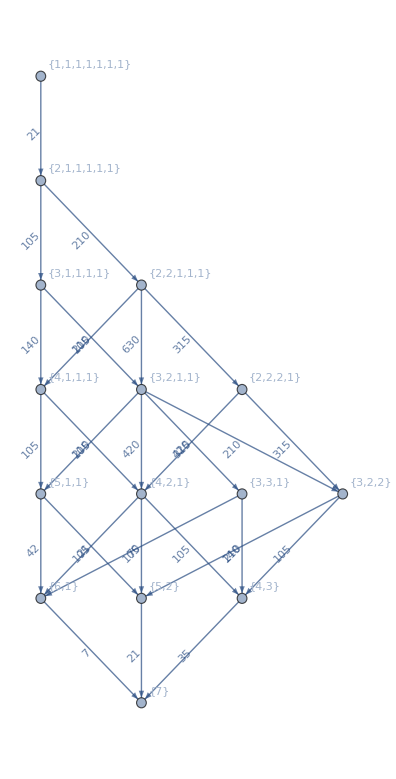

```mathematica
ReduceLattice[lattice]
```

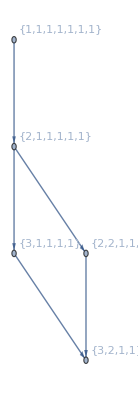

```mathematica
ReduceLattice[FormulaGraphReverse2[FindFullFormula[MinimalGraph[6]]]]
```

```mathematica
Ferrers[{{1,1}}]
```

{Posets`Private`UpFerrers[#1,{{1,1}}]&,{{1,1}},{1,1}}

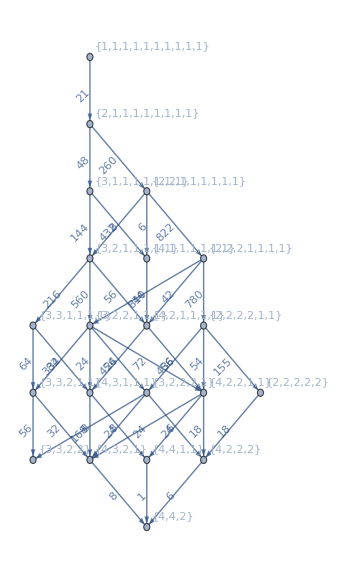

```mathematica
ReduceLattice[FormulaGraphReverse2[FindFullFormula[JacobsThalGraph[6]]]]
```

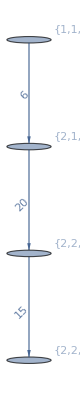

```mathematica
ReduceLattice[FormulaGraphReverse2[FindFullFormula[JacobsThalGraph[3]]]]
```

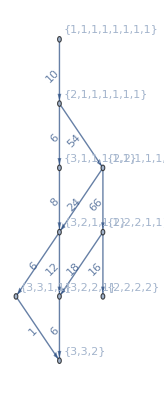

```mathematica
ReduceLattice[FormulaGraphReverse2[FindFullFormula[JacobsThalGraph[4]]]]
```

```mathematica
bigF=FindFullFormula[Graph[Range[8],{}]];
```

```mathematica
Length[bigF]
```

4140

```mathematica
bigFRev=FormulaGraphReverse2[bigF];
```

```mathematica
big=ReduceLattice[bigFRev];
```

```mathematica
small=ReduceLattice[FormulaGraphReverse2[FindFullFormula[JacobsThalGraph[4]]]];
```

```mathematica
Map[SymbolLevel,FindFullFormula[JacobsThalGraph[4]]]//Tally//Sort
```

{{3,1},{4,11},{5,30},{6,29},{7,10},{8,1}}

```mathematica
VertexCount[MinimalGraph[7]]
```

8

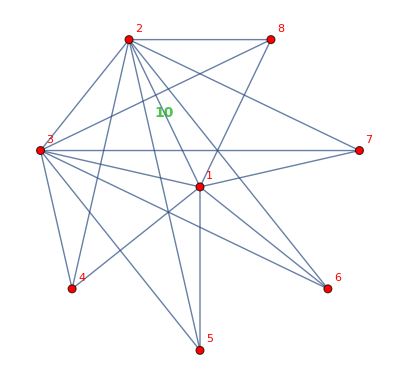
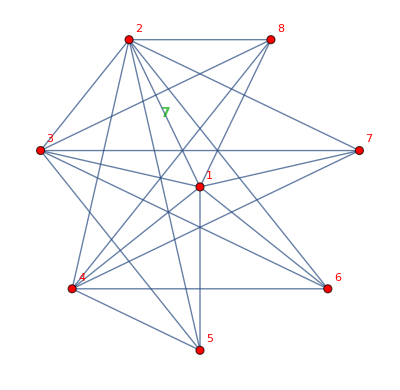
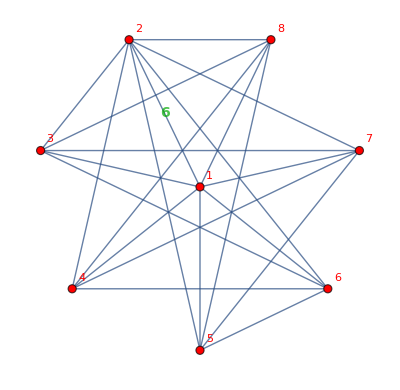
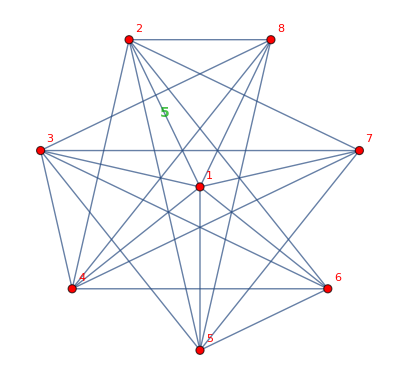
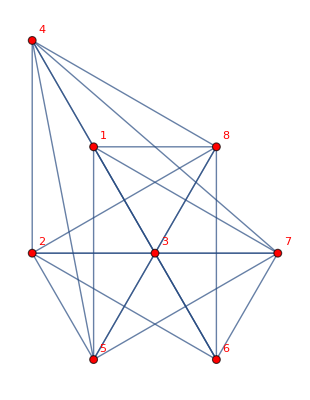

```mathematica
BarelyNColorableGraphsOfCount[8]
```

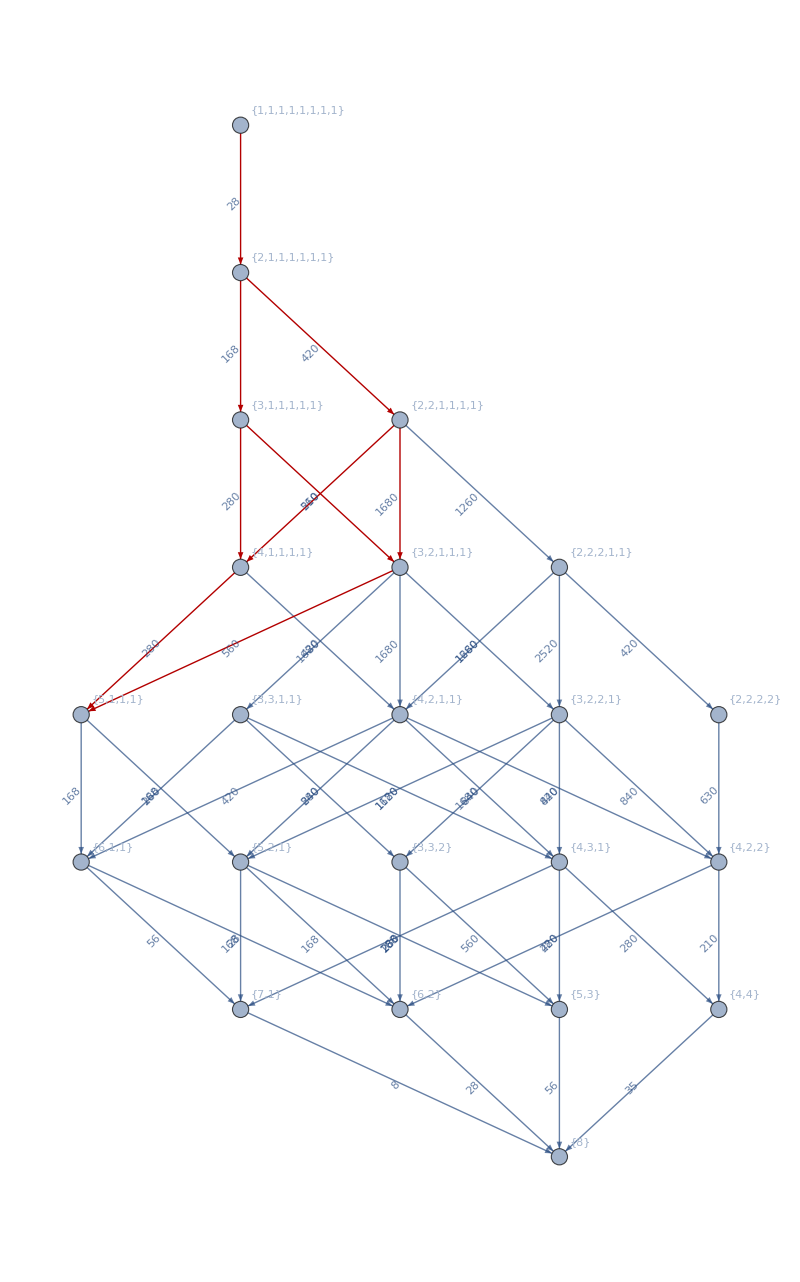
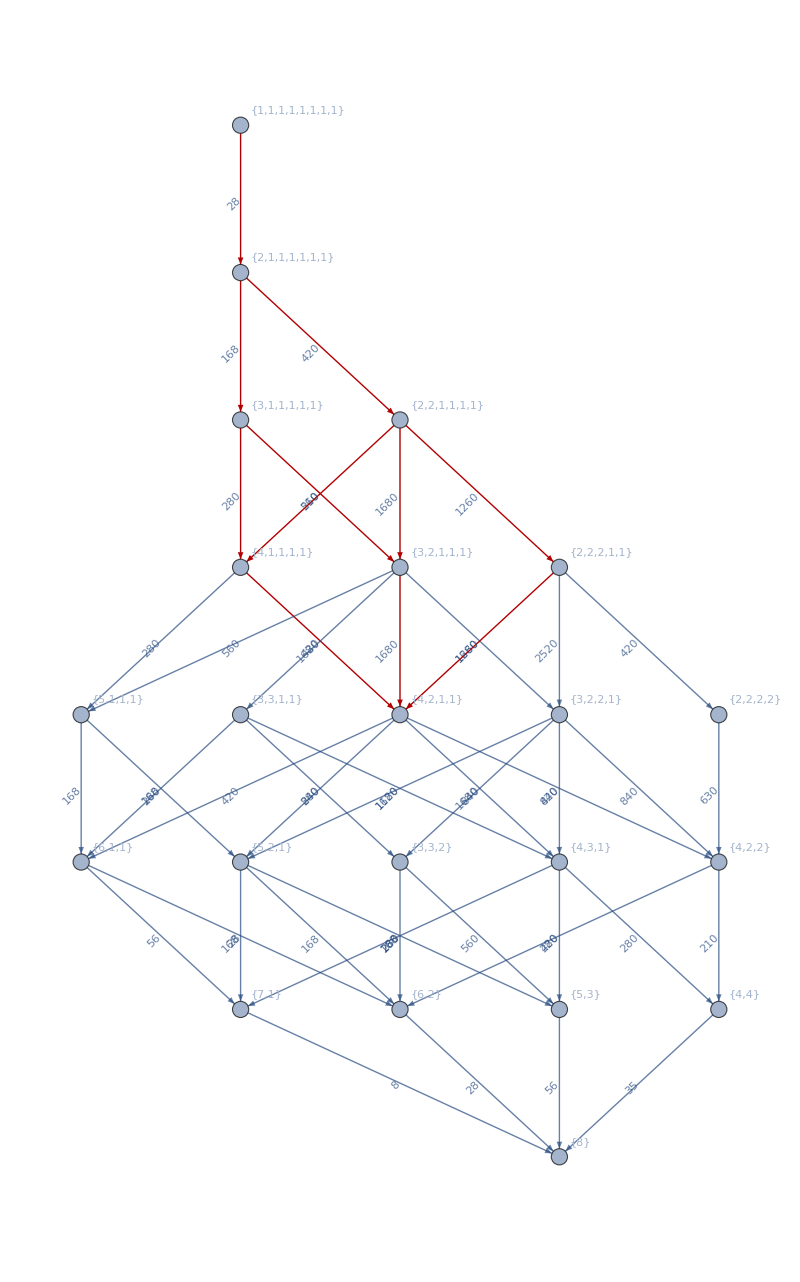
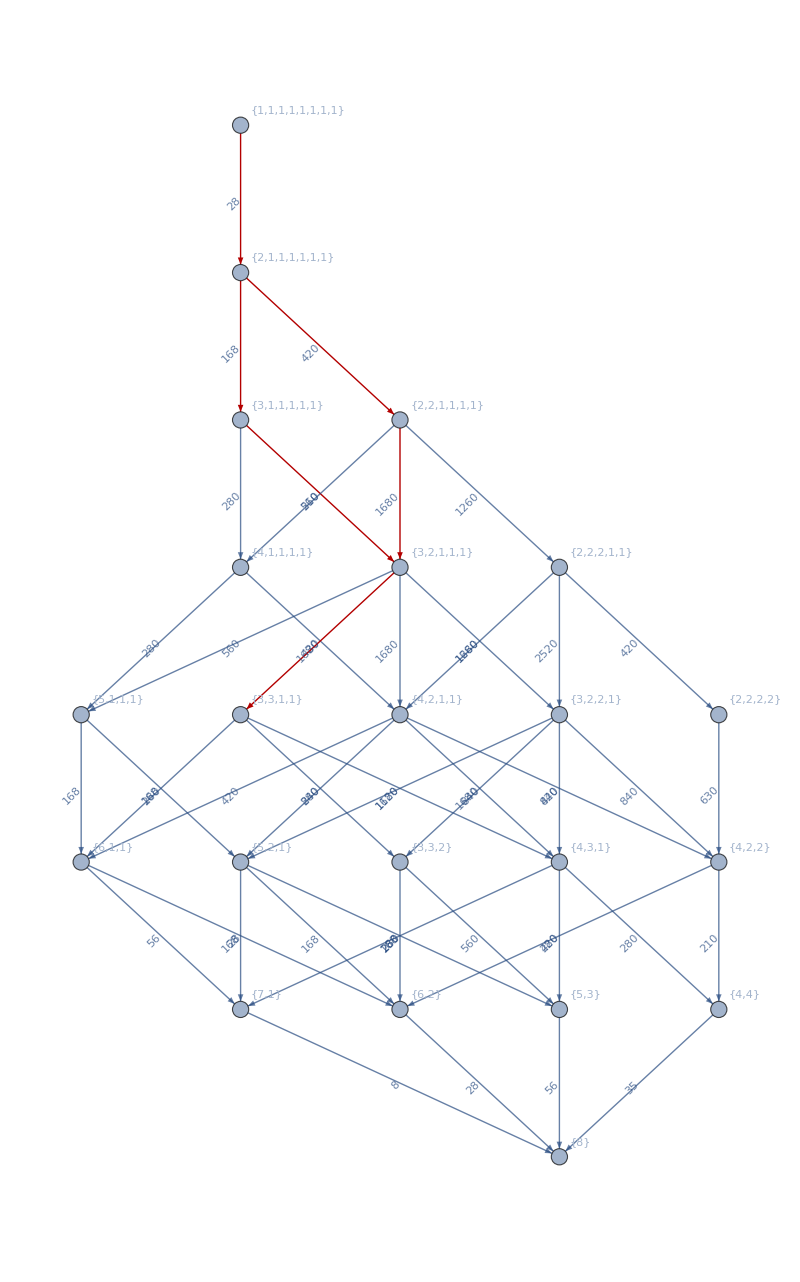
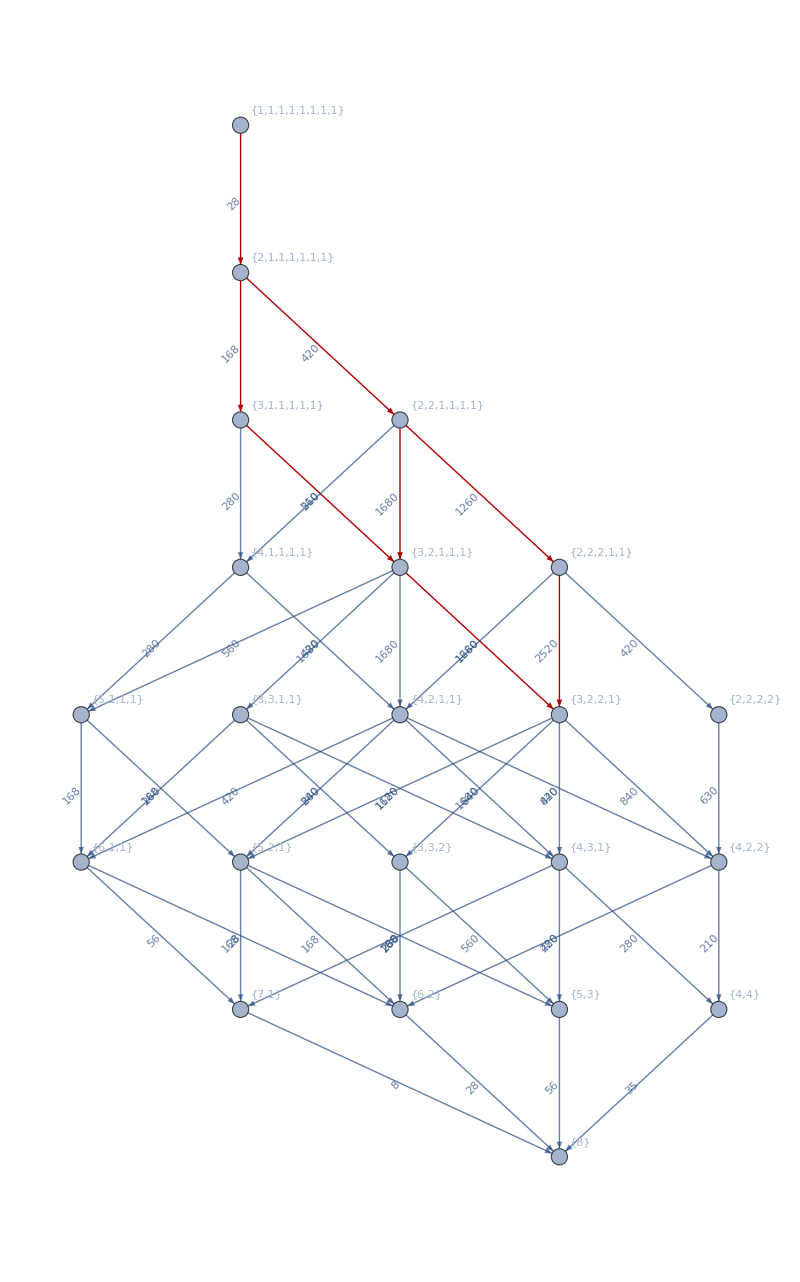
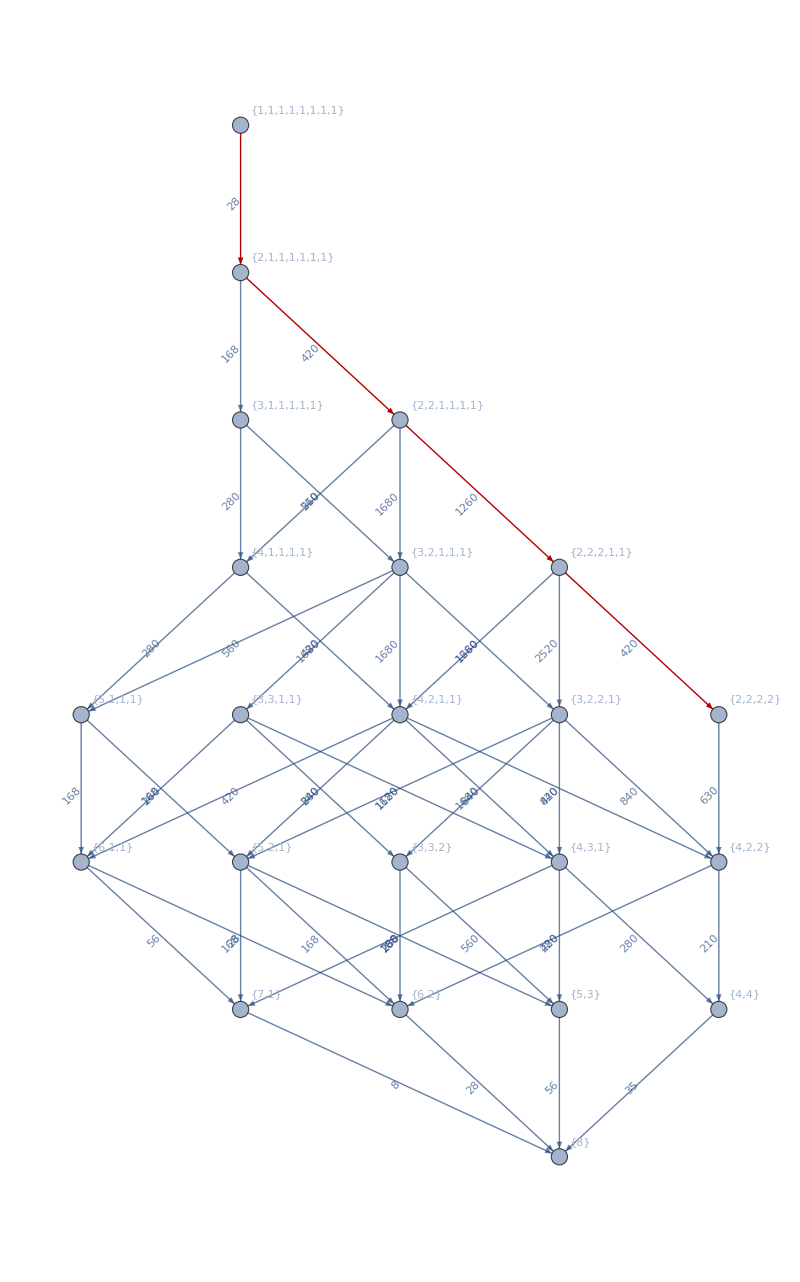

```mathematica
Table[
Graph[big,GraphHighlight->EdgeList[ReduceLattice[FormulaGraphReverse2[FindFullFormula[g]]]], GraphHighlightStyle->"Thick", ImageSize->800, AspectRatio->GoldenRatio],
{g,BarelyNColorableGraphsOfCount[8]}
]
```

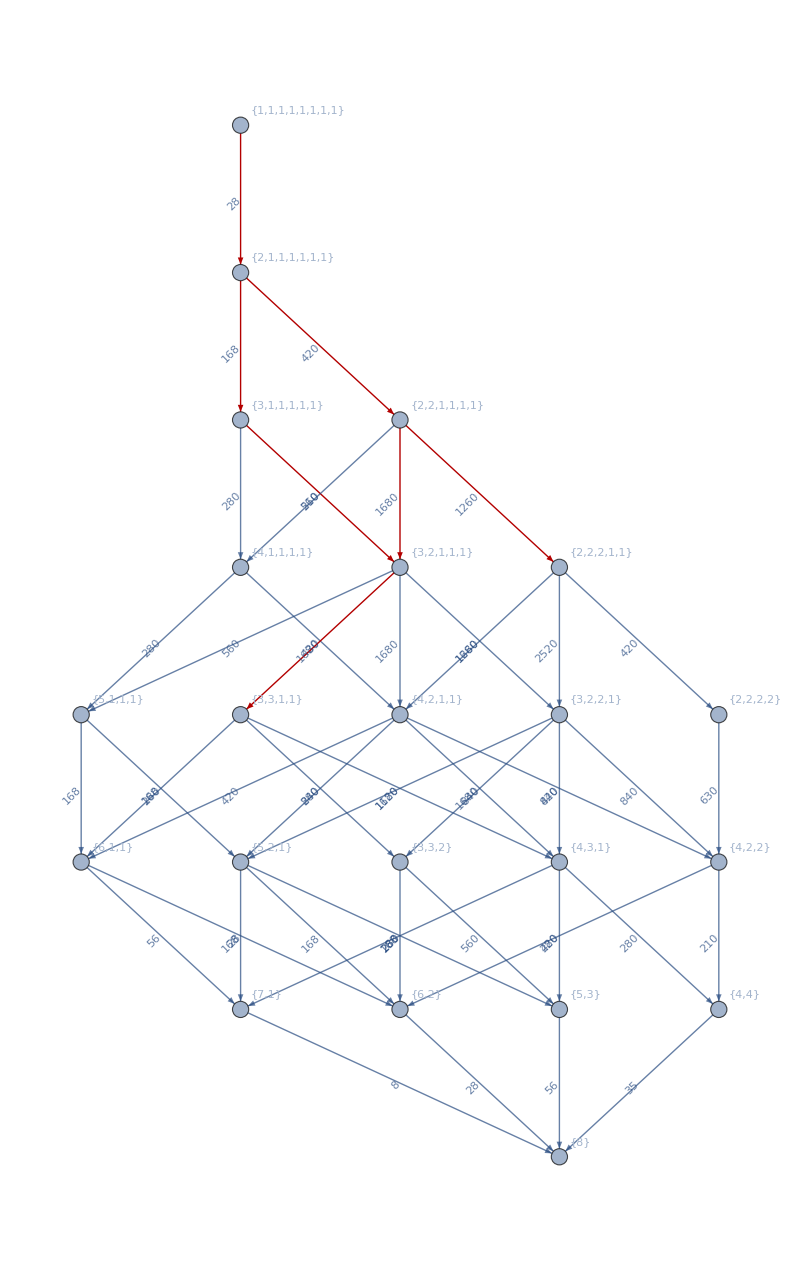

```mathematica
Graph[big,GraphHighlight->EdgeList[ReduceLattice[FormulaGraphReverse2[FindFullFormula[MinimalGraph[7]]]]], GraphHighlightStyle->"Thick", ImageSize->800, AspectRatio->GoldenRatio]
```

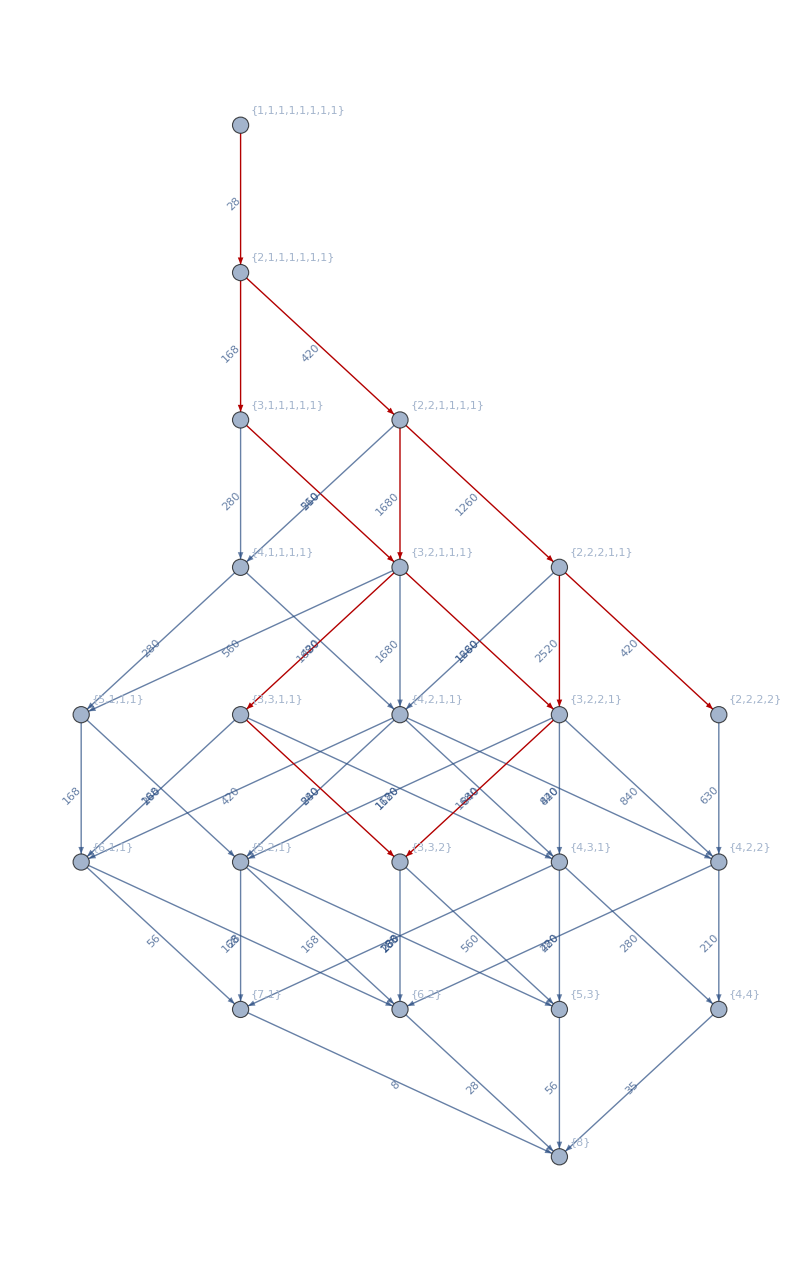

```mathematica
Graph[big,GraphHighlight->EdgeList[small], GraphHighlightStyle->"Thick", ImageSize->800, AspectRatio->GoldenRatio]
```

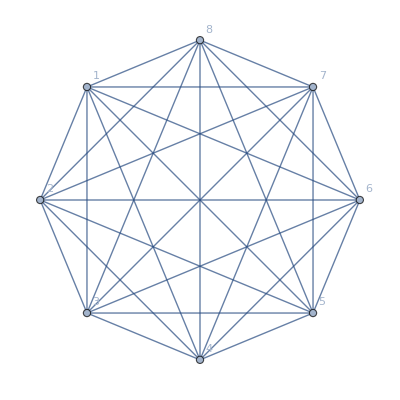
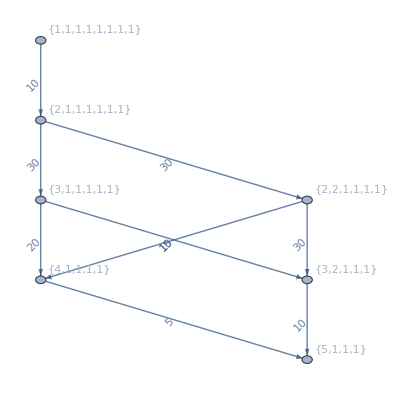
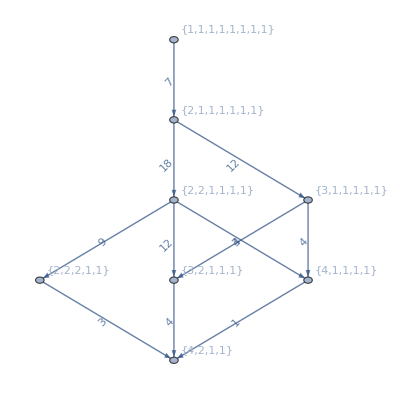
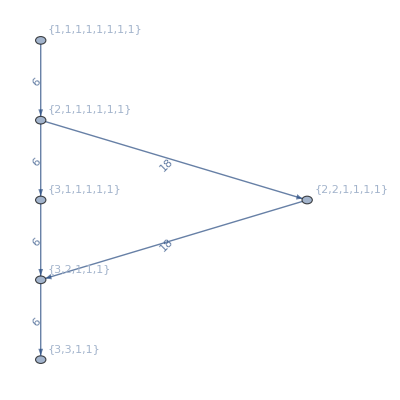
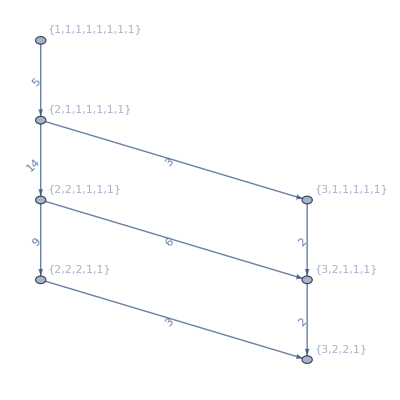
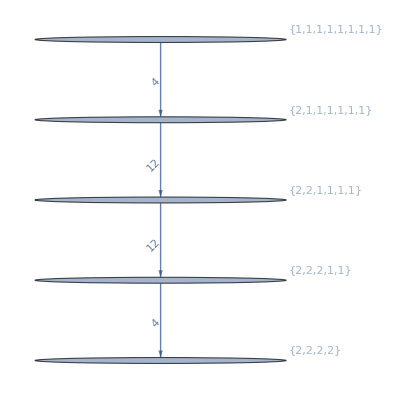
{-Graphics-{18,18}→-Graphics-7,-Graphics-{18,21}→-Graphics-8,-Graphics-{18,22}→-Graphics-6,-Graphics-{18,23}→-Graphics-7,-Graphics-{18,24}→-Graphics-5}

```mathematica
Table[
Labeled[CompleteGraph[VertexCount[g],GraphHighlight->EdgeList[GraphComplement[g]],GraphHighlightStyle->"Thick",VertexLabels->"Name"],{Style[With[{n=VertexCount[g]},3n-6],Bold,Darker[Green]],Style[EdgeCount[g],Bold,Red]}]->With[{h=Graph[ReduceLattice[FormulaGraphReverse2[FindFullFormula[g]]],ImageSize->{400,400},AspectRatio->GoldenRatio]},
Labeled[h,Style[VertexCount[h],Bold]]],
{g,BarelyNColorableGraphsOfCount[8]}
]
```

```mathematica
BarelyNColorableGraphsOfCount[8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FindRange[k_,min_:1,max_:300000]:=FindRange[k,min,max]=Block[{middle, size, bound1, bound2, pos},
middle=IntegerPart[(max+min)/2];
size=VertexCount[ReadGrof[middle]];
If[size< k,
FindRange[k,middle+1,max],
If[k< size,
FindRange[k,min,middle-1]
,
bound1=middle;
bound2=middle;
Monitor[
For[pos=middle-1, pos≥ min, pos--,
size=VertexCount[ReadGrof[pos]];
If[size==k,bound1--, Break[]]
],
{pos,min}
];
Monitor[
For[pos=middle+1, pos≤max, pos++,
size=VertexCount[ReadGrof[pos]];
If[size==k,bound2++, Break[]]
],
{pos,max}
];
{bound1,bound2}
]
]
]
```

```mathematica
FindRange[13]
```

$Aborted

```mathematica
Table[VertexCount[ReadGrof[k]],{k,9,24}]
```

{7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9}

```mathematica
EdgeList[-Graphics-]
```

{1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,2<->3,2<->4,2<->5,2<->6,2<->7,2<->8,3<->5,3<->6,3<->7,3<->8,4<->5,4<->6,4<->7,4<->8,5<->7,5<->8,6<->7,6<->8}

```mathematica
FindRange[8]
```

{10,23}

```mathematica
Range[FindRange[8]]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}}

```mathematica
Table[k<->Sort[Tally[Map[PartitionType[SymbolToSets[#]]&,FindFullFormula[ReadGrof[k]]]]],{k,With[{r=FindRange[8]},Range[r[[1]],r[[2]]]]}]
```

{10<->{{{2,2,2,2},1},{{2,2,2,1,1},15},{{2,2,1,1,1,1},25},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},11<->{{{2,2,2,2},3},{{3,2,2,1},2},{{2,2,2,1,1},22},{{3,2,1,1,1},3},{{2,2,1,1,1,1},27},{{3,1,1,1,1,1},1},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},12<->{{{3,2,2,1},1},{{2,2,2,1,1},12},{{3,2,1,1,1},3},{{2,2,1,1,1,1},24},{{3,1,1,1,1,1},1},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},13<->{{{3,2,2,1},1},{{2,2,2,1,1},10},{{3,2,1,1,1},5},{{2,2,1,1,1,1},23},{{3,1,1,1,1,1},2},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},14<->{{{2,2,2,2},1},{{3,2,2,1},3},{{2,2,2,1,1},18},{{3,2,1,1,1},4},{{2,2,1,1,1,1},26},{{3,1,1,1,1,1},1},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},15<->{{{2,2,2,2},3},{{3,2,2,1},1},{{2,2,2,1,1},20},{{3,2,1,1,1},2},{{2,2,1,1,1,1},26},{{3,1,1,1,1,1},1},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},16<->{{{3,2,2,1},1},{{2,2,2,1,1},9},{{3,2,1,1,1},6},{{2,2,1,1,1,1},22},{{3,1,1,1,1,1},3},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},17<->{{{2,2,2,2},1},{{2,2,2,1,1},12},{{3,2,1,1,1},3},{{2,2,1,1,1,1},23},{{3,1,1,1,1,1},2},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},18<->{{{2,2,2,2},3},{{2,2,2,1,1},26},{{2,2,1,1,1,1},29},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},19<->{{{2,2,2,2},4},{{2,2,2,1,1},22},{{2,2,1,1,1,1},27},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},20<->{{{2,2,2,2},2},{{3,2,2,1},2},{{2,2,2,1,1},18},{{3,2,1,1,1},4},{{2,2,1,1,1,1},25},{{3,1,1,1,1,1},2},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},21<->{{{3,3,2},1},{{2,2,2,2},4},{{3,2,2,1},6},{{3,3,1,1},1},{{2,2,2,1,1},22},{{3,2,1,1,1},8},{{2,2,1,1,1,1},27},{{3,1,1,1,1,1},2},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},22<->{{{3,3,1,1},1},{{2,2,2,1,1},5},{{3,2,1,1,1},10},{{2,2,1,1,1,1},21},{{3,1,1,1,1,1},4},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}},23<->{{{2,2,2,2},1},{{2,2,2,1,1},10},{{3,2,1,1,1},4},{{4,1,1,1,1},1},{{2,2,1,1,1,1},21},{{3,1,1,1,1,1},4},{{2,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1},1}}}

```mathematica
MissingEdges[ReadGrof[10]]
```

{{v15x28x34x67,1<->8},{v15x28x34x67,1<->4},{v15x28x34x67,1<->6},{v15x28x34x67,2<->4},{v15x28x34x67,7<->8},{v15x28x34x67,4<->7}}

```mathematica
Map[Last,MissingEdges[ReadGrof[10]]]
```

{1<->8,1<->4,1<->6,2<->4,7<->8,4<->7}

```mathematica
Factor[ChromaticPolynomial[EdgeAdd[ReadGrof[10],{1<->8,1<->4,1<->6,2<->4,7<->8,4<->7}],x]]
```

(-3+x) (-2+x) (-1+x) x (465-392 x+125 x^2-18 x^3+x^4)

```mathematica
With[{g=ReadGrof[23]},
With[{edges=MissingEdges[g]},
Table[
Factor[ChromaticPolynomial[EdgeContract[EdgeAdd[g,Map[Last,edges]],e],x]],
{e,Map[Last,edges]}
]
]
]
```

{(-4+x) (-3+x) (-2+x) (-1+x) x (21-9 x+x^2),(-4+x) (-3+x) (-2+x) (-1+x) x (21-9 x+x^2),(-4+x) (-3+x) (-2+x) (-1+x) x (21-9 x+x^2),(-4+x) (-3+x) (-2+x) (-1+x) x (21-9 x+x^2),(-4+x) (-3+x) (-2+x) (-1+x) x (21-9 x+x^2),(-4+x) (-3+x) (-2+x) (-1+x) x (21-9 x+x^2)}

```mathematica
MissingEdges2[ReadGrof[10],v15x28x34x67]
```

```mathematica
Clear[g]
```

```mathematica
Table[k<->
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[8]},Range[r[[1]],r[[2]]]]}
]
```

{10<->{{2,2,2,2}<->6},11<->{{2,2,2,2}<->6,{2,2,2,2}<->6,{3,2,2,1}<->5,{2,2,2,2}<->6,{3,2,2,1}<->5},12<->{{3,2,2,1}<->5},13<->{{3,2,2,1}<->5},14<->{{3,2,2,1}<->5,{3,2,2,1}<->5,{3,2,2,1}<->5,{2,2,2,2}<->6},15<->{{2,2,2,2}<->6,{2,2,2,2}<->6,{3,2,2,1}<->5,{2,2,2,2}<->6},16<->{{3,2,2,1}<->5},17<->{{2,2,2,2}<->6},18<->{{2,2,2,2}<->6,{2,2,2,2}<->6,{2,2,2,2}<->6},19<->{{2,2,2,2}<->6,{2,2,2,2}<->6,{2,2,2,2}<->6,{2,2,2,2}<->6},20<->{{2,2,2,2}<->6,{3,2,2,1}<->5,{3,2,2,1}<->5,{2,2,2,2}<->6},21<->{{3,2,2,1}<->5,{2,2,2,2}<->6,{2,2,2,2}<->6,{2,2,2,2}<->6,{3,2,2,1}<->5,{3,2,2,1}<->5,{3,2,2,1}<->5,{2,2,2,2}<->6,{3,3,1,1}<->4,{3,2,2,1}<->5,{3,2,2,1}<->5},22<->{{3,3,1,1}<->4},23<->{{2,2,2,2}<->6}}

```mathematica
Sort[Flatten[Table[
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[8]},Range[r[[1]],r[[2]]]]}
],1]]//Tally
```

{{{2,2,2,2}<->6,23},{{3,2,2,1}<->5,17},{{3,3,1,1}<->4,2}}

```mathematica
Sort[Flatten[Table[
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[7]},Range[r[[1]],r[[2]]]]}
],1]]//Tally
```

{{{2,2,2,1}<->3,11},{{3,2,1,1}<->2,1}}

```mathematica
Sort[Flatten[Table[
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[9]},Range[r[[1]],r[[2]]]]}
],1]]//Tally
```

{{{3,2,2,2}<->9,118},{{3,3,2,1}<->8,50},{{4,2,2,1}<->7,5},{{4,3,1,1}<->6,1}}

```mathematica
Sort[Flatten[Table[
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[10]},Range[r[[1]],r[[2]]]]}
],1]]//Tally
```

{{{3,3,2,2}<->13,708},{{3,3,3,1}<->12,76},{{4,2,2,2}<->12,96},{{4,3,2,1}<->11,67},{{4,4,1,1}<->9,2},{{5,2,2,1}<->9,1}}

```mathematica
Sort[Flatten[Table[
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[11]},Range[r[[1]],r[[2]]]]}
],1]]//Tally
```

{{{3,3,3,2}<->18,3208},{{4,3,2,2}<->17,2090},{{4,3,3,1}<->16,333},{{4,4,2,1}<->15,94},{{5,2,2,2}<->15,37},{{5,3,2,1}<->14,19},{{5,4,1,1}<->12,1}}

```mathematica
Sort[Flatten[Table[
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[12]},Range[r[[1]],r[[2]]]]}
],1]]//Tally
```

{{{3,3,3,3}<->24,8918},{{4,3,3,2}<->23,26786},{{4,4,2,2}<->22,3593},{{4,4,3,1}<->21,1195},{{5,3,2,2}<->21,1652},{{5,3,3,1}<->20,241},{{5,4,2,1}<->19,141},{{5,5,1,1}<->16,2},{{6,2,2,2}<->18,11},{{6,3,2,1}<->17,2}}

```mathematica
Sort[Flatten[Table[
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[13]},Range[r[[1]],r[[2]]]]}
],1]]//Tally
```

{{{4,3,3,3}<->30,154889},{{4,4,3,2}<->29,129366},{{4,4,4,1}<->27,2223},{{5,3,3,2}<->28,37498},{{5,4,2,2}<->27,10452},{{5,4,3,1}<->26,3392},{{5,5,2,1}<->24,177},{{6,3,2,2}<->25,696},{{6,3,3,1}<->24,87},{{6,4,2,1}<->23,45},{{6,5,1,1}<->20,1},{{7,2,2,2}<->21,2}}

```mathematica
Sort[Flatten[Table[
With[{g=ReadGrof[k]},
With[{form=FindFullFormula4[g]},
Table[
With[{edges=MissingEdges2[g,symbol]},
PartitionType[SymbolToSets[symbol]]<->Length[edges]
],
{symbol,form}
]
]
]
,{k,With[{r=FindRange[14]},Range[r[[1]],r[[2]]]]}
],1]]//Tally
```

$Aborted